```mathematica
HenonHeiles[{x0_,{y0_,dy0_},e_},tmax_]:=Module[{dx0=Sqrt[2/3 y0^3+2 e-x0^2-y0^2-2 x0^2 y0-dy0^2],x,y,t},Flatten[{x,y}/.NDSolve[{x''[t]==-x[t]-2 y[t] x[t],y''[t]==-y[t]-x[t]^2+y[t]^2,y[0]==y0,y'[0]==dy0,x[0]==x0,x'[0]==dx0},{x,y},{t,0,tmax},
Method->ExplicitRungeKutta,MaxSteps->5000]]]
```

```mathematica
SurfaceOfSection[{x0_,{y0_,dy0_},e_},tmax_]:=Module[{dx0=Sqrt[2/3 y0^3+2 e-x0^2-y0^2-2 x0^2 y0-dy0^2],x,y,t},If[#=={},{},First[#]]&@Last[Reap[NDSolve[{x''[t]==-x[t]-2 y[t] x[t],y''[t]==-y[t]-x[t]^2+y[t]^2,y[0]==y0,y'[0]==dy0,x[0]==x0,x'[0]==dx0},{x,y},{t,0,tmax},Method->{EventLocator,"Event"->x[t],"EventAction":>Sow[{y[t],y'[t]}]}]]]]
```

```mathematica
V[x_,y_]:=1/2 (x^2+y^2+2 x^2 y-2/3 y^3)

e[{x_,y_},t_]:=(x[t]^2+y[t]^2+2 x[t]^2 y[t]-2/3 y[t]^3+x'[t]^2+y'[t]^2)
```

```mathematica
Expand[{-D[V[x,y],x],-D[V[x,y],y]}];
```

```mathematica
Simplify[Solve[E==V[x,y]+(dx^2+dy^2)/2,dx]];
```

```mathematica
{xx,yy}=HenonHeiles[{0,{0.128846,0.018450},.125},100];
```

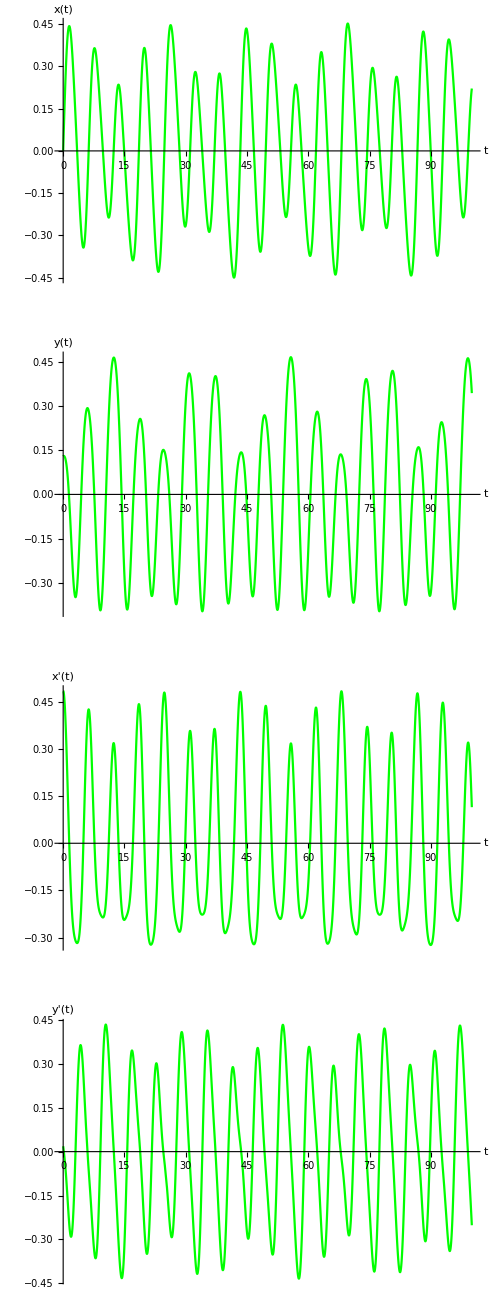

```mathematica
Show[GraphicsGrid[Partition[Plot[#[[1]][t],{t,0,100},DisplayFunction->Identity,PlotStyle->Green,
AxesLabel->TraditionalForm/@{t,#[[2]][t]}]&/@Transpose[{{xx,yy,xx',yy'},{x,y,x',y'}}],1]],
ImageSize->500]
```

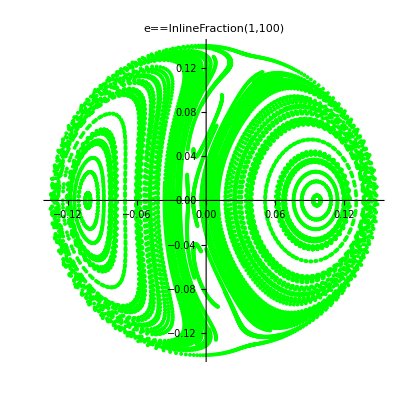
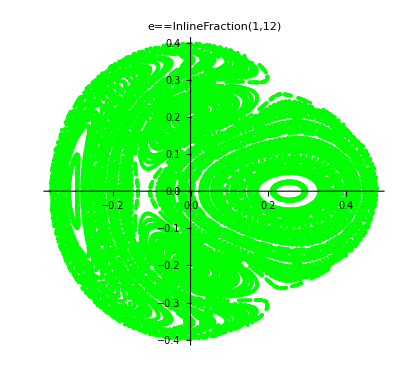
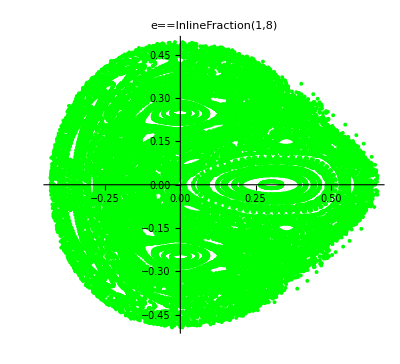

```mathematica
plots=Internal`DeactivateMessages[(x=If[#==1/100,x=.15,.3];
ListPlot[Join@@Table[SurfaceOfSection[{Random[Real,{-x,x}],
{Random[Real,{-x,x}],Random[Real,{-x,x}]},#},1000],{100}],
PlotStyle->{PointSize[.007],Green},AspectRatio->Automatic,PlotLabel->TraditionalForm[e==#/.Rational[n_,d_]:>InlineFraction[n,d]]])]&/@{1/100,1/12,1/8}
```